```mathematica
Ae := 0.09754278180  (*eV^0.9 cm^-3*)
κ:=0.17
Eerep:=511000 (*eV*)
Eemin:=1 10^6 (*eV*)(*1MeV*)
Eemax:=3.176*10^13(*eV*)
α:= 1.9
fvol:= 0.16
pc2cm:=3.0857 10^18
Rout:= 10*pc2cm(*cm*)
Rin:= 7.5*pc2cm(*cm*)
V:=4/3 π (Rout^3 - Rin^3)
k:=8.61*10^-5;      (*eV/kelvin*)
T:=2.7 (*Kelvin*)
h:=4.13*10^-15(*eV s*)
σT:=0.66 10^-24 (*cm^2*)
Area:=4*π*(Rout^2-Rin^2)
erg2ev:=6.24*10^11
c:=3*10^10 (*cm/s*)
```

```mathematica
ϵph[Eph_]:=Eph/Eerep
ϵγ[Eγ_]:=Eγ/Eerep
γ[Ee_]:= Ee/Eerep
x[Ee_,Eph_,Eγ_]:= ϵγ[Eγ]/(4ϵph[Eph] γ[Ee]^2(1-ϵγ[Eγ]/γ[Ee]))
P[Ee_,Eph_,Eγ_]:=HeavisideTheta[1-x[Ee,Eph,Eγ]]HeavisideTheta[x[Ee,Eph,Eγ]-1/(4 γ[Ee]^2)]
f[Ee_,Eγ_,Eph_]:= (2x[Ee,Eph,Eγ] Log[x[Ee,Eph,Eγ]]+x[Ee,Eph,Eγ]+1-2 x[Ee,Eph,Eγ]^2+((4ϵph[Eph] γ[Ee] x[Ee,Eph,Eγ])^2(1-x[Ee,Eph,Eγ]))/(2 (1+4 ϵph[Eph] γ[Ee] x[Ee,Eph,Eγ])))P[Ee,Eph,Eγ]
σIC[Ee_,Eγ_,Eph_]:=(3σT)/(4*Eerep*ϵph[Eph] γ[Ee]^2)f[Ee,Eγ,Eph]
Iic[Ee_]:=  Ae*Ee^-α* ⅇ^(-Ee/Eemax)
nBB[Eph_]:=(8*π)/(h*c)^3*Eph^2(ⅇ^(Eph/(k*T))-1)^-1
```

NIntegrate::inumr: The integrand 1.70794\ Eph\ « 1 »\ « 1 »\ (1 + 5.0231×10^11\ (1 - « 22 »/« 1 »)/(1 - « 22 »/Ee)^2\ (1 + 1.00231×10^6/Plus[« 2 »]\ Ee)\ Ee^2 - « 22 »/« 1 »^2\ « 1 »\ « 1 » + 6.54309×10^16/(1 - « 22 »/Ee)\ Ee^2\ Eph + 1.30862×10^17\ Log[6.54309×10^16/(1 + Times[« 2 »])\ Ee^2\ Eph]/(1 - 1.00231×10^6/Ee)\ Ee^2\ Eph)/(-1 + ⅇ^4301.63\ Eph)\ Ee^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 0.023247}}.

General::stop: Further output of NIntegrate :: inumr will be suppressed during this calculation.

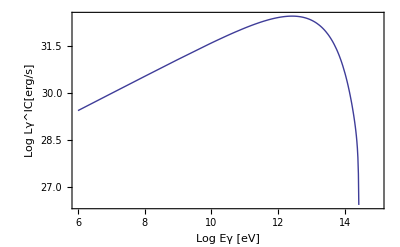

```mathematica
Plot[Log10[(10^Eγ)^2*fvol*V*c/(4π)*NIntegrate[NIntegrate[nBB[Eph]*σIC[Ee,10^Eγ,Eph],{Eph,0,100*k*T},AccuracyGoal->15]*Iic[Ee],{Ee,Eemin,10*Eemax},MaxRecursion->20]/erg2ev], {Eγ,6,15}, PlotPoints->10,Frame->True,FrameLabel->{"Log Eγ [eV]","Log Lγ^IC[erg/s]"},Axes->False]
```

## En Ergios

```mathematica
erg2ev:=6.24*10^11
Ae := 0.09754278180  (*eV^0.9 cm^-3*)
κ:=0.17
Eerep:=511000 (*eV*)
Eemin:=1 10^6 (*eV*)(*1MeV*)
Eemax:=3.176*10^13(*eV*)
α:= 1.9
fvol:= 0.16
pc2cm:=3.0857 10^18
Rout:= 10*pc2cm(*cm*)
Rin:= 7.5*pc2cm(*cm*)
V:=4/3 π (Rout^3 - Rin^3)
k:=8.61*10^-5;      (*eV/kelvin*)
T:=2.7 (*Kelvin*)
h:=4.13*10^-15(*eV s*)
σT:=0.66 10^-24 (*cm^2*)
Area:=4*π*(Rout^2-Rin^2)
c:=3*10^10 (*cm/s*)
```